### Imports

```mathematica
(* kill everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\Tal Miller\\Dropbox\\UNI\\Courses Graduate\\QFT\\Papers and Reviews\\Supersymmetric index and Localization\\Thesis\\Notebooks\\Star_shaped_quivers"];
```

```mathematica
<<"CharactersFunctions.m"
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\11.0\\AddOns\\Applications\\LieART\\LieART.m"]
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
maxVarNum=6;
a=Table[Subscript["a",i],{i,maxVarNum}];
b=Table[Subscript["b",i],{i,maxVarNum}];
$Assumptions={r>0,r<1};
```

### Haar measures examples

```mathematica
algebraClass=A;
rank=2;
```

```mathematica
haarMeas=haarMeasure[a,algebraClass,rank,type->"Short"]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2)

```mathematica
haarMeas=haarMeasure[a,algebraClass,rank,type->"Long"]
```

((1-1/(a_1 a_2^2)) (1-1/(a_1^2 a_2)) (1-a_1/a_2) (1-a_2/a_1) (1-a_1^2 a_2) (1-a_1 a_2^2))/(6 a_1 a_2)

### SU(2) chars

#### Rep {1} (fundamental)

```mathematica
algebraClass=A;
repDynkinLabels={1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

2

a_1+1/a_1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r/a_1) (1-a_1 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

calculation time = 0.015625 seconds = 4.34028×10^-6 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

Numeric divergence degree is 0.

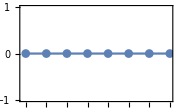

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1} + Rep {1}

```mathematica
algebraClass=A;
repDynkinLabels={1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

2

a_1+1/a_1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

(1-a_1^2)/(a_1 (1-r/a_1)^2 (1-a_1 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

calculation time = 0.015625 seconds = 4.34028×10^-6 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

Numeric divergence degree is -0.998006

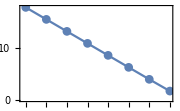

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2} (adjoint)

```mathematica
algebraClass=A;
repDynkinLabels={2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1^2+1/a_1^2+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r) (1-r/a_1^2) (1-a_1^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

calculation time = 0.0625 seconds = 0.0000173611 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### Rep {2}+Rep {2}

```mathematica
algebraClass=A;
repDynkinLabels={2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=  2 dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

2 (a_1^2+1/a_1^2+1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r)^2 (1-r/a_1^2)^2 (1-a_1^2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

calculation time = 0.03125 seconds = 8.68056×10^-6 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^3)

Numeric divergence degree is -2.99402

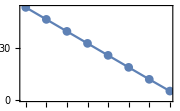

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {3}

```mathematica
algebraClass=A;
repDynkinLabels={3};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1^3+a_1+1/a_1+1/a_1^3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r/a_1^3) (1-r/a_1) (1-a_1 r) (1-a_1^3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

calculation time = 0.265625 seconds = 0.0000737847 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^4)

Numeric divergence degree is -0.994119

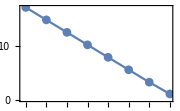

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {4}

```mathematica
algebraClass=A;
repDynkinLabels={4};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

5

a_1^4+a_1^2+1/a_1^2+1/a_1^4+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r) (1-r/a_1^4) (1-r/a_1^2) (1-a_1^2 r) (1-a_1^4 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

calculation time = 0.359375 seconds = 0.0000998264 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(r^5-r^3-r^2+1)

Numeric divergence degree is -1.99405

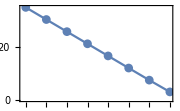

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {5}

```mathematica
algebraClass=A;
repDynkinLabels={5};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1^5+a_1^3+a_1+1/a_1+1/a_1^3+1/a_1^5

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r/a_1^5) (1-r/a_1^3) (1-r/a_1) (1-a_1 r) (1-a_1^3 r) (1-a_1^5 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 10

Calculating residue for pole 1/10 in level 1

Calculating residue for pole 2/10 in level 1

Calculating residue for pole 3/10 in level 1

Calculating residue for pole 4/10 in level 1

Calculating residue for pole 5/10 in level 1

Calculating residue for pole 6/10 in level 1

Calculating residue for pole 7/10 in level 1

Calculating residue for pole 8/10 in level 1

Calculating residue for pole 9/10 in level 1

Calculating residue for pole 10/10 in level 1

calculation time = 1.125 seconds = 0.0003125 hours

Numeric divergence degree is -2.98315

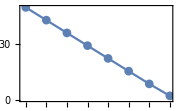

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {6}

```mathematica
algebraClass=A;
repDynkinLabels={6};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

7

a_1^6+a_1^4+a_1^2+1/a_1^2+1/a_1^4+1/a_1^6+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r) (1-r/a_1^6) (1-r/a_1^4) (1-r/a_1^2) (1-a_1^2 r) (1-a_1^4 r) (1-a_1^6 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 13

Calculating residue for pole 1/13 in level 1

Calculating residue for pole 2/13 in level 1

Calculating residue for pole 3/13 in level 1

Calculating residue for pole 4/13 in level 1

Calculating residue for pole 5/13 in level 1

Calculating residue for pole 6/13 in level 1

Calculating residue for pole 7/13 in level 1

Calculating residue for pole 8/13 in level 1

Calculating residue for pole 9/13 in level 1

Calculating residue for pole 10/13 in level 1

Calculating residue for pole 11/13 in level 1

Calculating residue for pole 12/13 in level 1

Calculating residue for pole 13/13 in level 1

calculation time = 1.17188 seconds = 0.000325521 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

((r-1) r (r+1) (r^2+1) (r^3+r^2-1)+1)/((r-1)^4 (r+1)^3 (r^2+1) (r^2+r+1) (r^4+r^3+r^2+r+1))

Numeric divergence degree is -3.98605

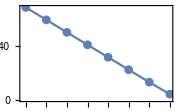

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {7}

```mathematica
algebraClass=A;
repDynkinLabels={7};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_1^7+a_1^5+a_1^3+a_1+1/a_1+1/a_1^3+1/a_1^5+1/a_1^7

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r/a_1^7) (1-r/a_1^5) (1-r/a_1^3) (1-r/a_1) (1-a_1 r) (1-a_1^3 r) (1-a_1^5 r) (1-a_1^7 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 17

Calculating residue for pole 1/17 in level 1

Calculating residue for pole 2/17 in level 1

Calculating residue for pole 3/17 in level 1

Calculating residue for pole 4/17 in level 1

Calculating residue for pole 5/17 in level 1

Calculating residue for pole 6/17 in level 1

Calculating residue for pole 7/17 in level 1

Calculating residue for pole 8/17 in level 1

Calculating residue for pole 9/17 in level 1

Calculating residue for pole 10/17 in level 1

Calculating residue for pole 11/17 in level 1

Calculating residue for pole 12/17 in level 1

Calculating residue for pole 13/17 in level 1

Calculating residue for pole 14/17 in level 1

Calculating residue for pole 15/17 in level 1

Calculating residue for pole 16/17 in level 1

Calculating residue for pole 17/17 in level 1

calculation time = 2.4375 seconds = 0.000677083 hours

Numeric divergence degree is -4.99309

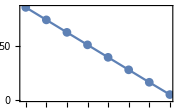

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {8}

```mathematica
algebraClass=A;
repDynkinLabels={8};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

9

a_1^8+a_1^6+a_1^4+a_1^2+1/a_1^2+1/a_1^4+1/a_1^6+1/a_1^8+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

(1-a_1^2)/(a_1 (1-r) (1-r/a_1^8) (1-r/a_1^6) (1-r/a_1^4) (1-r/a_1^2) (1-a_1^2 r) (1-a_1^4 r) (1-a_1^6 r) (1-a_1^8 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 21

Calculating residue for pole 1/21 in level 1

Calculating residue for pole 2/21 in level 1

Calculating residue for pole 3/21 in level 1

Calculating residue for pole 4/21 in level 1

Calculating residue for pole 5/21 in level 1

Calculating residue for pole 6/21 in level 1

Calculating residue for pole 7/21 in level 1

Calculating residue for pole 8/21 in level 1

Calculating residue for pole 9/21 in level 1

Calculating residue for pole 10/21 in level 1

Calculating residue for pole 11/21 in level 1

Calculating residue for pole 12/21 in level 1

Calculating residue for pole 13/21 in level 1

Calculating residue for pole 14/21 in level 1

Calculating residue for pole 15/21 in level 1

Calculating residue for pole 16/21 in level 1

Calculating residue for pole 17/21 in level 1

Calculating residue for pole 18/21 in level 1

Calculating residue for pole 19/21 in level 1

Calculating residue for pole 20/21 in level 1

Calculating residue for pole 21/21 in level 1

calculation time = 2.625 seconds = 0.000729167 hours

Numeric divergence degree is -5.98958

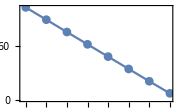

```mathematica
calcNumericDivergence[hilbertComponents]
```

### SU(2) + U(1) chars

#### SU(2) rep {1} + rep {1} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

2

a_1+1/a_1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

(1-a_1^2)/(a_1 t (1-r/(a_1 t)) (1-(r t)/a_1) (1-(a_1 r)/t) (1-a_1 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is zero.

Residue for pole 2/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.078125 seconds = 0.0000217014 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### SU(2) rep {2} + rep {2} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1^2+1/a_1^2+1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

(1-a_1^2)/(a_1 t (1-r/t) (1-r t) (1-r/(a_1^2 t)) (1-(r t)/a_1^2) (1-(a_1^2 r)/t) (1-a_1^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 1

Calculating residue for pole 2/4 in level 1

Calculating residue for pole 3/4 in level 1

Calculating residue for pole 4/4 in level 1

Residue for pole 1/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 2/4 in level 1 is zero.

Residue for pole 3/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 4/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.296875 seconds = 0.0000824653 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/((r^2-1)^2 (r^2+1))

Numeric divergence degree is -1.99213

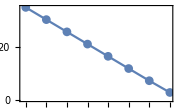

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### SU(2) rep {1} + SU(2) singlet with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

2

a_1+1/a_1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

(1-a_1^2)/(a_1 t (1-r/t) (1-(r t)/a_1) (1-a_1 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.0625 seconds = 0.0000173611 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is 0.

-Graphics-

#### SU(2) rep {2} + singlet with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1^2+1/a_1^2+1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

(1-a_1^2)/(a_1 t (1-r/t) (1-r t) (1-(r t)/a_1^2) (1-a_1^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.046875 seconds = 0.0000130208 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^4)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.994119

-Graphics-

#### SU(2) rep {3} + singlet with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={3};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1^3+a_1+1/a_1+1/a_1^3

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

(1-a_1^2)/(a_1 t (1-r/t) (1-(r t)/a_1^3) (1-(r t)/a_1) (1-a_1 r t) (1-a_1^3 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.25 seconds = 0.0000694444 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^8)

Numeric divergence degree is -0.986744

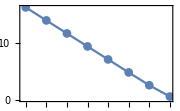

```mathematica
calcNumericDivergence[hilbertComponents]
```